```mathematica
DSolve[{y''[x]+2*y'[x]/x+y[x]^5==0,y[0]==1,y'[0]==0},y[x],x]
```

DSolve::bvimp: 通解包含隐式解. 在边值问题中，这些解将被忽略，因此某些解可能会丢失.

{}

```mathematica
{{y[x]->BesselJ[0,(2 x^(3/2))/3]}}
BesselJ[0,(2 x^(3/2))/3]
```

{{y[x]→BesselJ[0,(2 x^(3/2))/3]}}

```mathematica
s=NDSolve[{y''[x]+2/x*y'[x]+y[x]^(3/2)==0,y[0.0001]==1,y'[0.0001]==0},y[x],{x,0.001,20}]
```

{{y[x]→InterpolatingFunction[…][x]}}

InterpolatingFunction::dmval: 输入值 {0.000612857} 位于插值函数的数据范围之外. 将使用外推法.

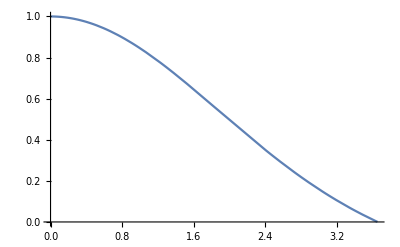

FindRoot::nlnum: 在 {x} = {3.65375+1.7889×10^-11 ⅈ} 处，函数值 {«1»} 不是由数字组成的维度为 {1} 的列表.

{x→3.65356+0. ⅈ}

InterpolatingFunction::dmval: 输入值 {0.0102041} 位于插值函数的数据范围之外. 将使用外推法.

InterpolatingFunction::dmval: 输入值 {0.214082} 位于插值函数的数据范围之外. 将使用外推法.

InterpolatingFunction::dmval: 输入值 {0.417959} 位于插值函数的数据范围之外. 将使用外推法.

General::stop: 在本次计算中，InterpolatingFunction::dmval 的进一步输出将被抑制.

-Graphics-

FindRoot::nlnum: 在 {x} = {2.} 处，函数值 {y[2.]→0.582851} 不是由数字组成的维度为 {1} 的列表.

FindRoot[s,{x,2}]

```mathematica
Plot[Evaluate[y[x]/.s],{x,0,30},PlotRange->All]
FindRoot[Evaluate[y[x]/.s],{x,2}]
```

```mathematica
000
```

```mathematica
00
```

0

```mathematica
0
```

0

```mathematica
.0
```

```mathematica
0.0.0000
```

0.